## Integration #2

## Jacob Russell

## 1) Write algorithms

```mathematica
simpsons[a_,b_,f_]:=Module[{},Return[(b-a)/6(f[a]+4f[(a+b)/2]+f[b])]];
trapezoid[a_,b_,f_]:=Module[{},Return[1/2(b-a)(f[a]+f[b])]];
simpsons38[a_,b_,f_]:=Module[{},Return[(3(b-a))/16(f[a]+3f[a+(b-a)/2]+3f[a+(b-a)]+f[b])]];
```

```mathematica
AQ[a0_,b0_,f_,ξ_,integralRule_]:=Module[{a=N[a0],b=N[b0],c=0},
c=(a+b)/2.;
k=k+1;
rab=integralRule[a,b,f];
rac=integralRule[a,c,f];
rcb=integralRule[c,b,f];
If[Abs[rab-(rac+rcb)]<ξ,
Return[rac + rcb],
Return[AQ[a,c,f,ξ,integralRule]+AQ[c,b,f,ξ/2,integralRule]]]];
```

## 2) Estimate integrals

```mathematica
f1[x_]=ⅇ^(-x^3); (* from [-2,3] *)
```

```mathematica
f2[x_]=x*Sin[x^2]; (* from [0,25] *)
```

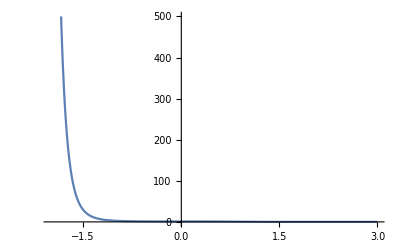

```mathematica
f3[x_]=Cos[x^2]Log[x^2+5] ⅇ^x; (* from [-4,4] *)

Plot[f1[x],{x,-2,3},PlotRange->{0,500}]
```

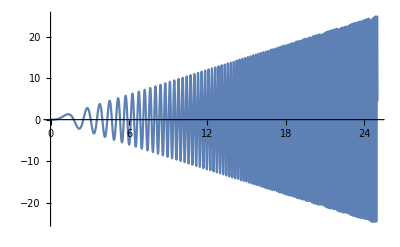

```mathematica
Plot[f2[x],{x,0,25}]
```

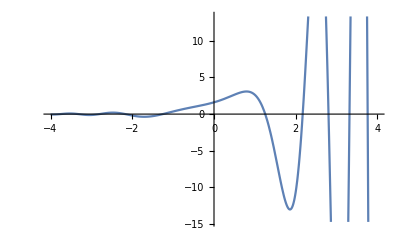

```mathematica
Plot[f3[x],{x,-4,4}]
```

```mathematica
k=0;
```

```mathematica
AQ[-2,3,f1,.001,simpsons]
```

277.746

```mathematica
NIntegrate[f1[x],{x,-2,3}]
```

277.746

```mathematica
k
```

61